```mathematica
DataFileName="/Users/magse/workspace/pcb_layout_demo_eo/BRD1622119324405675.csv";
```

```mathematica
Timing[data=Import[DataFileName];]
```

{27.8209,Null}

```mathematica
LEDColor[r_]:=ColorData["Pastel",r/8.0]
```

```mathematica
PlotFrame[d_]:=Show[Graphics[{LightGreen,Annulus[{0,0},{20,100},{0,π/2}]},Axes->True],Graphics[Table[Partition[{LEDColor[d⟦5+n⟧],Disk[{d⟦3+n⟧,d⟦4+n⟧},d⟦5+n⟧]},2],{n,1,Length[d]-4,3}],Axes->True],AspectRatio->1,PlotRange->{{-200,+200},{-200,+200}},Frame->True,FrameStyle->Directive[GrayLevel[0,0.2],Thickness[Medium],ImageSize->Large]]
```

```mathematica
PlotFrame[data⟦-1⟧]
```

-Graphics-

```mathematica
ListLinePlot[Log10[data⟦All,2⟧],PlotRange->All]
```

-Graphics-

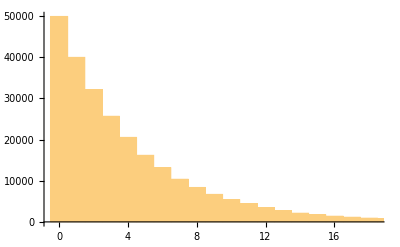

```mathematica
Histogram[data⟦All,3⟧,{1}]
```

```mathematica
Timing[Export[StringReplace[DataFileName,".csv"->".mov"],ListAnimate[Table[PlotFrame[data⟦n⟧],{n,1,Length[data⟦All,1⟧],1000}],AnimationRate->12,ControlPlacement->Bottom, AppearanceElements->None]]]
```

{119.342,/Users/magse/workspace/pcb_layout_demo_eo/BRD1622116548841671.mov}